```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=1;
r=0.2;
cr={0.45,0.55};
ys[x_]:=cr+r{Cos[2 π x/L],Sin[2 π x /L]}
```

```mathematica
(*check for ys*)
```

```mathematica
ys=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/solution/ys.csv"][[2;;]]
```

```mathematica
(*points for the vector field*)
```

```mathematica
ys=Table[{ys[[i,1]],ys[[i,2]]},{i,1,Length[ys]}]
```

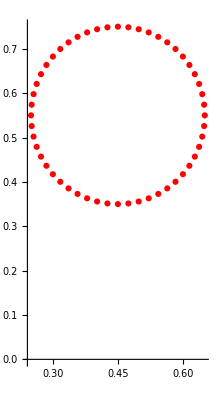

```mathematica
ListPlot[ys,AspectRatio->Automatic,PlotStyle->Red]
```